## The classical ground state of zigzag phase for alpha-RuCl3

```mathematica
pKxy=-5.5;
pKz=−5.5;
pΓxy=7.6;
pΓz=7.6;
pθ=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
pϕ=Pi/4;
pJ=2.17;
```

```mathematica
H0[θ_,ϕ_]:=pKxy Sin[θ]^2-pKz Cos[θ]^2+pΓxy Sin[2 θ](Sin[ϕ]+Cos[ϕ])-pΓz Sin[2 ϕ] Sin[θ]^2
```

```mathematica
θ1=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2;
θ2=ArcTan[-2Sqrt[2] pΓxy/(pKxy+pKz-pΓz)]/2+Pi/2;
```

```mathematica
plot=Plot3D[H0[x,y],{x,0,Pi},{y,0,2Pi}];
p1=Graphics3D[{Red,PointSize[0.05],Point[{θ1,Pi/4,H0[θ1,Pi/4]}]}];
p2=Graphics3D[{Blue,PointSize[0.05],Point[{θ2,Pi/4,H0[θ2,Pi/4]}]}];
Show[plot,p1,p2]
```

-Graphics3D-

## The Spin Wave Function

#### Local coordinate for spins in ground state

```mathematica
Z[1]={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Z[2]={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Z[3]=-{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Z[4]=-{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
```

```mathematica
X[1]={Sin[ϕ],-Cos[ϕ],0};
X[2]={Sin[ϕ],-Cos[ϕ],0};
X[3]=-{Sin[ϕ],-Cos[ϕ],0};
X[4]=-{Sin[ϕ],-Cos[ϕ],0};
```

```mathematica
Cross[{1,0,0},{0,1,0}]
```

{0,0,1}

```mathematica
For[i=1,i≤4,i++,Y[i]=Simplify[Cross[Z[i],X[i]]]]
```

```mathematica
For[i=1,i≤4,i++,S[i]=S0[i]Z[i]+SX[i] X[i]+ SY[i] Y[i]]
```

```mathematica
MatrixForm[IdentityMatrix[3]]
```

```mathematica
BJ=J({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
BX=({{Kxy, 0, 0}, {0, 0, Γxy}, {0, Γxy, 0}})+BJ;
BY=({{0, 0, Γxy}, {0, Kxy, 0}, {Γxy, 0, 0}})+BJ;
BZ=({{0, Γz, 0}, {Γz, 0, 0}, {0, 0, Kz}})+BJ;
```

```mathematica
MatrixForm[Table[m n, {m,{a,b,c,d}},{n,{e,f,g,h}}]]
```

```mathematica
hamiltonian=Simplify[S[1].BY.S[2]+Exp[-I qb]S[1].BX.S[2]+Exp[-I qa-I qb]S[1].BZ.S[4]+S[2].BZ.S[3]+S[3].BY.S[4]+Exp[-I qb]S[3].BX.S[4]];
```

```mathematica
MatrixForm[Simplify[Table[SeriesCoefficient[hamiltonian,{m,0,1},{n,0,1}],{m,{SX[1],SY[1],SX[2],SY[2],SX[3],SY[3],SX[4],SY[4]}},{n,{SX[1],SY[1],SX[2],SY[2],SX[3],SY[3],SX[4],SY[4]}}]]]
```

```mathematica
UPH=({{0, 0, (J+Kxy) Cos[ϕ]^2+1/2 ⅇ^(-ⅈ qb) (2 J+Kxy-Kxy Cos[2 ϕ])+J Sin[ϕ]^2, -Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J+Γz Sin[2 ϕ]), -ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ]}, {0, 0, -Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])), 0, 0, ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ], ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]))}, {0, 0, 0, 0, -J+Γz Sin[2 ϕ], -Γz Cos[θ] Cos[2 ϕ], 0, 0}, {0, 0, 0, 0, Γz Cos[θ] Cos[2 ϕ], (J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]), 0, 0}, {0, 0, 0, 0, 0, 0, 1/2 ⅇ^(-ⅈ qb) ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)+(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ]), Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ])}, {0, 0, 0, 0, 0, 0, Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ]))}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})
```

{{0,0,(J+Kxy) Cos[ϕ]^2+1/2 ⅇ^(-ⅈ qb) (2 J+Kxy-Kxy Cos[2 ϕ])+J Sin[ϕ]^2,-Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]),0,0,ⅇ^(-ⅈ (qa+qb)) (-J+Γz Sin[2 ϕ]),-ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ]},{0,0,-Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]),ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])),0,0,ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ],ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]))},{0,0,0,0,-J+Γz Sin[2 ϕ],-Γz Cos[θ] Cos[2 ϕ],0,0},{0,0,0,0,Γz Cos[θ] Cos[2 ϕ],(J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]),0,0},{0,0,0,0,0,0,1/2 ⅇ^(-ⅈ qb) ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)+(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ]),Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ])},{0,0,0,0,0,0,Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]),ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ]))},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[Simplify[Table[SeriesCoefficient[hamiltonian,{m,0,1}],{m,{S0[1],S0[2],S0[3],S0[4]}}]]]
```

(Γxy Cos[θ] Cos[ϕ] S0[2] Sin[θ]+Γxy Cos[θ] Sin[ϕ] SX[2]+Γxy Cos[θ]^2 Cos[ϕ] SY[2]+Γxy Cos[ϕ] Sin[θ] (Cos[θ] S0[2]-Sin[θ] SY[2])+Kxy Sin[θ] Sin[ϕ] (S0[2] Sin[θ] Sin[ϕ]-Cos[ϕ] SX[2]+Cos[θ] Sin[ϕ] SY[2])+ⅇ^(-ⅈ qb) (Cos[ϕ] (-Γxy Cos[θ]+Kxy Sin[θ] Sin[ϕ]) SX[2]+Kxy Cos[ϕ]^2 Sin[θ] (S0[2] Sin[θ]+Cos[θ] SY[2])+Γxy Sin[ϕ] (S0[2] Sin[2 θ]+Cos[2 θ] SY[2]))+ⅇ^(-ⅈ (qa+qb)) (-Kz Cos[θ]^2 S0[4]+Γz Sin[θ] (-2 Cos[ϕ] S0[4] Sin[θ] Sin[ϕ]+Cos[ϕ]^2 SX[4]-Sin[ϕ]^2 SX[4])-Cos[θ] Sin[θ] (Kz-Γz Sin[2 ϕ]) SY[4])
-Kz Cos[θ]^2 S0[3]+Γxy Cos[θ] Cos[ϕ] S0[1] Sin[θ]+Γxy Cos[θ] Sin[ϕ] SX[1]+Γxy Cos[θ]^2 Cos[ϕ] SY[1]+Γxy Cos[ϕ] Sin[θ] (Cos[θ] S0[1]-Sin[θ] SY[1])+Kxy Sin[θ] Sin[ϕ] (S0[1] Sin[θ] Sin[ϕ]-Cos[ϕ] SX[1]+Cos[θ] Sin[ϕ] SY[1])+ⅇ^(-ⅈ qb) (Cos[ϕ] (-Γxy Cos[θ]+Kxy Sin[θ] Sin[ϕ]) SX[1]+Kxy Cos[ϕ]^2 Sin[θ] (S0[1] Sin[θ]+Cos[θ] SY[1])+Γxy Sin[ϕ] (S0[1] Sin[2 θ]+Cos[2 θ] SY[1]))-Kz Cos[θ] Sin[θ] SY[3]+Γz Cos[ϕ] Sin[θ] (-S0[3] Sin[θ] Sin[ϕ]+Cos[ϕ] SX[3]+Cos[θ] Sin[ϕ] SY[3])-Γz Sin[θ] Sin[ϕ] (Sin[ϕ] SX[3]+Cos[ϕ] (S0[3] Sin[θ]-Cos[θ] SY[3]))
-Kz Cos[θ]^2 S0[2]+Γxy Cos[θ] Cos[ϕ] S0[4] Sin[θ]+Γxy Cos[θ] Sin[ϕ] SX[4]+Kz Cos[θ] Sin[θ] SY[2]+Γz Cos[ϕ] Sin[θ] (-S0[2] Sin[θ] Sin[ϕ]+Cos[ϕ] SX[2]-Cos[θ] Sin[ϕ] SY[2])-Γz Sin[θ] Sin[ϕ] (Sin[ϕ] SX[2]+Cos[ϕ] (S0[2] Sin[θ]+Cos[θ] SY[2]))-Γxy Cos[θ]^2 Cos[ϕ] SY[4]+Γxy Cos[ϕ] Sin[θ] (Cos[θ] S0[4]+Sin[θ] SY[4])+Kxy Sin[θ] Sin[ϕ] (S0[4] Sin[θ] Sin[ϕ]-Cos[ϕ] SX[4]-Cos[θ] Sin[ϕ] SY[4])+ⅇ^(-ⅈ qb) (Cos[ϕ] (-Γxy Cos[θ]+Kxy Sin[θ] Sin[ϕ]) SX[4]+Kxy Cos[ϕ]^2 Sin[θ] (S0[4] Sin[θ]-Cos[θ] SY[4])+Γxy Sin[ϕ] (S0[4] Sin[2 θ]-Cos[2 θ] SY[4]))
Γxy Cos[θ] Cos[ϕ] S0[3] Sin[θ]+Γxy Cos[θ] Sin[ϕ] SX[3]+ⅇ^(-ⅈ (qa+qb)) (-Kz Cos[θ]^2 S0[1]+Γz Sin[θ] (-2 Cos[ϕ] S0[1] Sin[θ] Sin[ϕ]+Cos[ϕ]^2 SX[1]-Sin[ϕ]^2 SX[1])+Cos[θ] Sin[θ] (Kz-Γz Sin[2 ϕ]) SY[1])-Γxy Cos[θ]^2 Cos[ϕ] SY[3]+Γxy Cos[ϕ] Sin[θ] (Cos[θ] S0[3]+Sin[θ] SY[3])+Kxy Sin[θ] Sin[ϕ] (S0[3] Sin[θ] Sin[ϕ]-Cos[ϕ] SX[3]-Cos[θ] Sin[ϕ] SY[3])+ⅇ^(-ⅈ qb) (Cos[ϕ] (-Γxy Cos[θ]+Kxy Sin[θ] Sin[ϕ]) SX[3]+Kxy Cos[ϕ]^2 Sin[θ] (S0[3] Sin[θ]-Cos[θ] SY[3])+Γxy Sin[ϕ] (S0[3] Sin[2 θ]-Cos[2 θ] SY[3])))

```mathematica
FullSimplify[Γxy Cos[θ] Cos[ϕ]  Sin[θ]+Γxy Cos[ϕ] Sin[θ] (Cos[θ] )+Kxy Sin[θ] Sin[ϕ] ( Sin[θ] Sin[ϕ])+ ((Kxy Cos[ϕ]^2 Sin[θ] (Sin[θ]))+Γxy Sin[ϕ] (Sin[2 θ]))+(-Kz Cos[θ]^2 S0[4]+Γz Sin[θ] (-2 Cos[ϕ]  Sin[θ] Sin[ϕ]))]
```

```mathematica
FullSimplify[-Kz Cos[θ]^2 +Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])]
```

```mathematica
-(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ]))/2
```

```mathematica
MatrixForm[Simplify[UPH+ConjugateTranspose[UPH],Assumptions->Element[{qa,qb,Kxy,Kz,Γxy,Γz,θ,ϕ,J},Reals]]]
```

(0 | 0 | (J+Kxy) Cos[ϕ]^2+1/2 ⅇ^(-ⅈ qb) (2 J+Kxy-Kxy Cos[2 ϕ])+J Sin[ϕ]^2 | -Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]) | 0 | 0 | ⅇ^(-ⅈ (qa+qb)) (-J+Γz Sin[2 ϕ]) | -ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ]
0 | 0 | -Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]) | ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])) | 0 | 0 | ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ] | ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]))
(J+Kxy) Cos[ϕ]^2+1/2 ⅇ^(ⅈ qb) (2 J+Kxy-Kxy Cos[2 ϕ])+J Sin[ϕ]^2 | -Γxy Sin[θ] Sin[ϕ]+Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]) | 0 | 0 | -J+Γz Sin[2 ϕ] | -Γz Cos[θ] Cos[2 ϕ] | 0 | 0
-Γxy Sin[θ] Sin[ϕ]+Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]) | ⅇ^(ⅈ qb) Conjugate[1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])] | 0 | 0 | Γz Cos[θ] Cos[2 ϕ] | (J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]) | 0 | 0
0 | 0 | -J+Γz Sin[2 ϕ] | Γz Cos[θ] Cos[2 ϕ] | 0 | 0 | 1/2 ⅇ^(-ⅈ qb) ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)+(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ]) | Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ])
0 | 0 | -Γz Cos[θ] Cos[2 ϕ] | (J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]) | 0 | 0 | Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]) | ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ]))
ⅇ^(ⅈ (qa+qb)) (-J+Γz Sin[2 ϕ]) | ⅇ^(ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ] | 0 | 0 | 1/2 ⅇ^(ⅈ qb) Conjugate[(1+ⅇ^(ⅈ qb)) (2 J+Kxy)+(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ]] | Γxy Sin[θ] Sin[ϕ]-Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]) | 0 | 0
-ⅇ^(ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ] | ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ])) | 0 | 0 | Γxy Sin[θ] Sin[ϕ]-Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]) | ⅇ^(ⅈ qb) Conjugate[1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])] | 0 | 0)

```mathematica
MatrixForm[KroneckerProduct[IdentityMatrix[4],PauliMatrix[2]]]
```

(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0)

```mathematica
H[qa_,qb_,Kxy_,Kz_,Γxy_,Γz_,θ_,ϕ_,J_]:=(1/2)({{0, -ⅈ, 0, 0, 0, 0, 0, 0}, {ⅈ, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, ⅈ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -ⅈ, 0, 0}, {0, 0, 0, 0, ⅈ, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -ⅈ}, {0, 0, 0, 0, 0, 0, ⅈ, 0}}).({{-(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J), 0, (J+Kxy) Cos[ϕ]^2+1/2 ⅇ^(-ⅈ qb) (2 J+Kxy-Kxy Cos[2 ϕ])+J Sin[ϕ]^2, -Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), 0, 0, ⅇ^(-ⅈ (qa+qb)) (-J+Γz Sin[2 ϕ]), -ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ]}, {0, -(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J), -Γxy Sin[θ] Sin[ϕ]+ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])), 0, 0, ⅇ^(-ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ], ⅇ^(-ⅈ (qa+qb)) ((J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]))}, {(J+Kxy) Cos[ϕ]^2+1/2 ⅇ^(ⅈ qb) (2 J+Kxy-Kxy Cos[2 ϕ])+J Sin[ϕ]^2, -Γxy Sin[θ] Sin[ϕ]+Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), -(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J), 0, -J+Γz Sin[2 ϕ], -Γz Cos[θ] Cos[2 ϕ], 0, 0}, {-Γxy Sin[θ] Sin[ϕ]+Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), ⅇ^(ⅈ qb) Conjugate[1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])], 0, -(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J), Γz Cos[θ] Cos[2 ϕ], (J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]), 0, 0}, {0, 0, -J+Γz Sin[2 ϕ], Γz Cos[θ] Cos[2 ϕ], -(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J), 0, 1/2 ⅇ^(-ⅈ qb) ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)+(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ]), Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ])}, {0, 0, -Γz Cos[θ] Cos[2 ϕ], (J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ]), 0, -(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J), Γxy Sin[θ] Sin[ϕ]-ⅇ^(-ⅈ qb) Cos[ϕ] (Γxy Sin[θ]-(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), ⅇ^(-ⅈ qb) (1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ]))}, {ⅇ^(ⅈ (qa+qb)) (-J+Γz Sin[2 ϕ]), ⅇ^(ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ], 0, 0, 1/2 ⅇ^(ⅈ qb) Conjugate[(1+ⅇ^(ⅈ qb)) (2 J+Kxy)+(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ]], Γxy Sin[θ] Sin[ϕ]-Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), -(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J), 0}, {-ⅇ^(ⅈ (qa+qb)) Γz Cos[θ] Cos[2 ϕ], ⅇ^(ⅈ (qa+qb)) ((J+Kz) Sin[θ]^2+Cos[θ]^2 (J+Γz Sin[2 ϕ])), 0, 0, Γxy Sin[θ] Sin[ϕ]-Cos[ϕ] (ⅇ^(ⅈ qb) Γxy Sin[θ]+(-1+ⅇ^(ⅈ qb)) Kxy Cos[θ] Sin[ϕ]), ⅇ^(ⅈ qb) Conjugate[1/2 Cos[θ]^2 ((1+ⅇ^(ⅈ qb)) (2 J+Kxy)-(-1+ⅇ^(ⅈ qb)) Kxy Cos[2 ϕ])+(1+ⅇ^(ⅈ qb)) J Sin[θ]^2-Γxy Sin[2 θ] (ⅇ^(ⅈ qb) Cos[ϕ]+Sin[ϕ])], 0, -(-Kz Cos[θ]^2+Γxy Sin[2 θ] (Cos[ϕ]+Sin[ϕ])+Sin[θ]^2 (Kxy-Γz Sin[2 ϕ])+J)}})
```

```mathematica
HH[qa_,qb_]:=H[qa,qb,pKxy,pKz,pΓxy,pΓz,pθ,pϕ,pJ]
```

```mathematica
EE[qa_,qb_]:=Sort[Eigenvalues[HH[qa,qb]]]
```

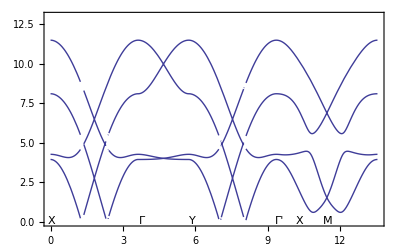

```mathematica
Plot[Piecewise[{{EE[0,(t-2Pi/Sqrt[3])Sqrt[3]],t≥0&&t<2Pi/Sqrt[3]},{EE[(t-2Pi/Sqrt[3])*3,0],t≥2Pi/Sqrt[3]&&t<(2Pi/Sqrt[3]+2Pi/3)},{EE[2Pi,Sqrt[3](t-(2Pi/Sqrt[3]+2Pi/3))],t≥(2Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/Sqrt[3]+2Pi/3)},{EE[3*((4Pi/Sqrt[3]+2Pi/3)-t)/2+2Pi,2Pi+3*((4Pi/Sqrt[3]+2Pi/3)-t)/2],t≥(4Pi/Sqrt[3]+2Pi/3)&&t<(4Pi/3+4Pi/Sqrt[3])},{EE[Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2,Pi+3*((4Pi/3+4Pi/Sqrt[3])-t)/2],t≥(4Pi/3+4Pi/Sqrt[3])&&t<(2Pi+4Pi/Sqrt[3])}}],{t,0,2Pi+4Pi/Sqrt[3]},GridLines->{{{2Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/Sqrt[3]+2Pi/3,Dashed},{4Pi/3+4Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["X",{0.05,0.08}],Inset["Γ",{2Pi/Sqrt[3]+0.15,0.08}],Inset["Y",{2Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["Γ'",{4Pi/Sqrt[3]+2Pi/3+0.15,0.08}],Inset["M",{4Pi/3+4Pi/Sqrt[3]+0.05,0.08}],Inset["X",{4Pi/3+2Pi-0.15,0.08}]},Frame->True,PlotRange->{{0,2Pi+4Pi/Sqrt[3]},{0,13}}]
```